p218

```mathematica
w[z_]:=Module[{s=√(z+1)√(z-1)},
1/π(s+Log[z+s])
]
TabView[{
"orig"->ParametricPlot[ReIm[x+ I y],{x, -10,4},{y,0,10},
PlotRange->All,Mesh->All],
"image"->ParametricPlot[ReIm[w[x+ I y]],{x, -10,4},{y,0,10},
PlotRange->All,Mesh->All]
},2]
```

12

p219

```mathematica
w[z_]:=Module[{s=√(z+1)√(z-1)},
2/π(s+ArcSin[1/z])
]
TabView[{
"orig"->ParametricPlot[ReIm[x+ I y],{x, -3,3},{y,0,2},
PlotRange->All,Mesh->All],
"image"->ParametricPlot[ReIm[w[x+ I y]],{x, -3,3},{y,0,2},
PlotRange->All,Mesh->All,
PlotPoints->100]
},2]
```

12

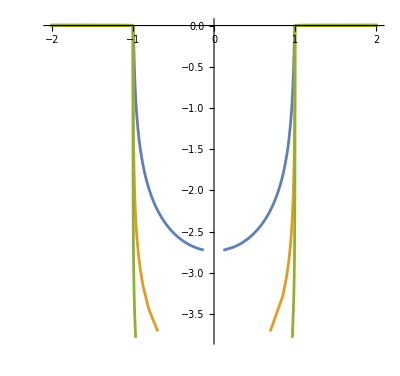

```mathematica
ϵ=10^-3;
ParametricPlot[Evaluate[Table[ReIm[w[x+ϵ I]],{ϵ,{0.01,0.001,0.0001}}]],{x,-3,3},PlotRange->All]
```

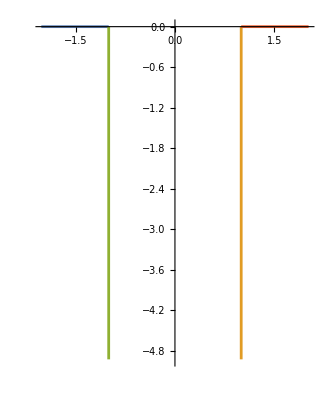

```mathematica
ParametricPlot[{
ReIm[w[-1-2x+10^-12 I]],
ReIm[w[x+10^-12 I]],
ReIm[w[-x+10^-12 I]],
ReIm[w[1+2x+10^-12 I]]
},{x,0,1},PlotRange->All]
```

p221

```mathematica
w[z_]:=0.5(z+1/z)
TabView[{
"orig"->ParametricPlot[ReIm[r E^(ⅈ θ)],{r, 1,6},{θ,0,π},
PlotRange->All,Mesh->All],
"image"->ParametricPlot[ReIm[w[r E^(ⅈ θ)]],{r, 1,6},{θ,0,π},
PlotRange->All,Mesh->All,
PlotPoints->20]
},2]
```

12

# Schwarz-Christoffel

If I have a bunch of points on the real axis 
	A_1<A_2<…<A_(n-1)<A_n=∞
and a bunch of positive exponents β_1,β_2,…,β_n satisfying 
	1<∑_(k=1)^n β_k
and define
	S[z]=∫_0^z 1/(∏_(k=1)^(n-1) (ζ-A_k)^β_k)dζ

Lets see what happens with A_(1:3)={0,1,∞} and β_(1:3)={0.5,0.5,0}

1/((-1.+ζ)^0.5 (0.+ζ)^0.5)

-2. Log[√(-1.+ζ)-1. √ζ]

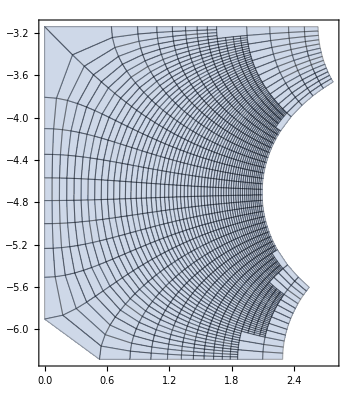

```mathematica
A={0.0,1.0,∞};
β={0.5,0.5,0};
n=Length[β];
SCIntegrand=Product[(ζ-A⟦i⟧)^(-β⟦i⟧),{i,1,n-1}]
SC[ζ_]=Integrate[SCIntegrand,ζ]

ParametricPlot[ReIm[SC[x+I y]],{x,-3,3},{y,0,2},
Mesh->All]
```